```mathematica
kw=10^-14;
Clear[f,g,m,n];
f[Pk1_,Pk2_,c_]:=-Log10[√((10^-Pk1(10^-Pk2*c+kw))/(10^-Pk1+c))];
g[Pk1_,Pk2_,c_]:=-Log10[√((10^-Pk1*10^-Pk2*c)/(10^-Pk1+c))];
m[Pk1_,Pk2_,c_]:=-Log10[√(10^-Pk1*10^-Pk2)];
n[Pk1_,Pk2_,c_]:=-Log10[√((10^-Pk1*10^-Pk2*c+10^-Pk1*kw)/c)];
```

```mathematica
Manipulate[Show[ContourPlot3D[10^-x+10^-PH==kw/10^-PH+10^-x((10^-PH*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2PH)+10^-PH*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,0,20},{Pk2,0,20},{PH,0,14},PlotTheme->"Scientific",ImageSize->Medium,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"accurate PH"},PlotRange->Full],Plot3D[g[Pk1,Pk2,10^-x],{Pk1,0,20},{Pk2,0,20},PlotTheme->"Scientific",ImageSize->Large,AxesLabel->Automatic,AxesStyle->Thick,PlotRange->Full,PlotStyle->Blue,PlotLegends->{"PH of H_x2"}]],{x,-2,14}]
```

```mathematica
Manipulate[Show[ContourPlot3D[10^-x+10^(-(PH-0.02))==kw/10^(-(PH-0.02))+10^-x((10^(-(PH-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH-0.02))+10^(-(PH-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,0,20},{Pk2,0,20},{PH,0,14},PlotTheme->"Scientific",ImageSize->Medium,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"sup for different concentration"},PlotRange->Full,ContourStyle->Green],Plot3D[g[Pk1,Pk2,10^-x],{Pk1,0,20},{Pk2,0,20},PlotTheme->"Scientific",ImageSize->Large,AxesLabel->Automatic,AxesStyle->Thick,PlotRange->Full,PlotStyle->Blue,PlotLegends->{"PH of H_x2"},Mesh->None]],{x,-2,14}]
Manipulate[Show[ContourPlot3D[10^-x+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+10^-x((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,0,20},{Pk2,0,20},{PH,0,14},PlotTheme->"Scientific",ImageSize->Medium,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"inf for different concentration"},PlotRange->Full,ContourStyle->Yellow],Plot3D[g[Pk1,Pk2,10^-x],{Pk1,0,20},{Pk2,0,20},PlotTheme->"Scientific",ImageSize->Large,AxesLabel->Automatic,AxesStyle->Thick,PlotRange->Full,PlotStyle->Blue,PlotLegends->{"PH of H_x2"},Mesh->None]],{x,-2,14}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {Pk1,Pk2,PH} = {3.39,10.944,7.17568}. Try perturbing the initial point(s).

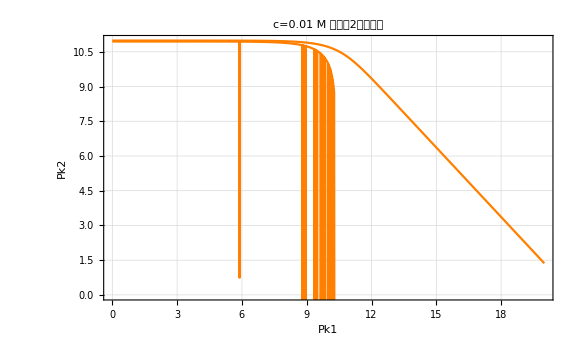

```mathematica
c=0.01;
cp2sup=Table[{a,FindRoot[{c+10^(-(PH-0.02))==kw/10^(-(PH-0.02))+c((10^(-(PH-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH-0.02))+10^(-(PH-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==-Log10[√((10^-Pk1*10^-Pk2*c)/(10^-Pk1+c))],Pk1==a},{Pk1,a},{Pk2,20},{PH,20},WorkingPrecision->MachinePrecision][[2,2]]},{a,0,20,0.01}];
cp2supline=ListLinePlot[cp2sup,PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[c=0.01M 时公式2的可行域],LabelStyle->{GrayLevel[0]},ImageSize->Large];

cp2inf=Table[{a,FindRoot[{c+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+c((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==-Log10[√((10^-Pk1*10^-Pk2*c)/(10^-Pk1+c))],Pk1==a},{Pk1,a},{Pk2,20},{PH,20},WorkingPrecision->MachinePrecision][[2,2]]},{a,0,20,0.01}];
cp2infline=ListLinePlot[cp2inf,PlotTheme->"Detailed",PlotStyle->Orange,FrameLabel->{{HoldForm[Pk2],None},{HoldForm[Pk1],None}},PlotLabel->HoldForm[c=0.01M 时公式2的可行域],LabelStyle->{GrayLevel[0]},ImageSize->Large];
Show[cp2supline,cp2infline]
```

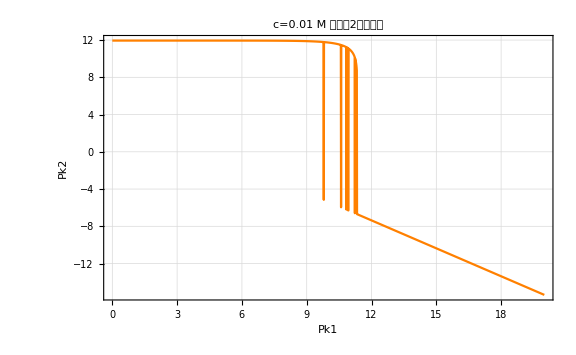

```mathematica
Show[cp2infline]
```

```mathematica
Solve[{Pk1==10,c+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+c((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==-Log10[√((10^-Pk1*10^-Pk2*c)/(10^-Pk1+c))]},{Pk1,Pk2,PH},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pk1→10.,Pk2→-3.36588,PH→3.31706}}

```mathematica
c==0.01;
Solve[{c+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+c((10^(-(PH+0.02))*10^-10+2*10^-10*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-10+10^-10*10^-Pk2)),PH==-Log10[√((10^-10*10^-Pk2*c)/(10^-10+c))]},{Pk2,PH},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pk2→-5.36588,PH→2.31706}}

```mathematica
NSolve[{Pk1==10,c+10^(-(PH+0.02))==kw/10^(-(PH+0.02))+c((10^(-(PH+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(PH+0.02))+10^(-(PH+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),PH==-Log10[√((10^-Pk1*10^-Pk2*c)/(10^-Pk1+c))]},{Pk1,Pk2,PH},Reals,WorkingPrecision->100]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Pk1→10.,Pk2→-3.36588,PH→3.31706}}

```mathematica
cp2supsurface=ContourPlot3D[10^-Pc+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))==kw/(10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02)))+10^-Pc*((10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},ContourStyle->{RGBColor[0.5864078175768783, 0.26359194937432395, 0.519486597936422],Opacity[0.5]},ImageSize->Medium,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"surface for sup"},PlotRange->Full,PlotTheme->"Scientific",Mesh->None];
```

```mathematica
cp2infsurface=ContourPlot3D[10^-Pc+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))==kw/(10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02)))+10^-Pc*((10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-1,20},{Pk2,-5,16},{Pc,-1,7},ContourStyle->{RGBColor[0.5355579515419151, 0.9430131641554946, 0.004882822085237493],Opacity[0.5]},ImageSize->Medium,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"surface for sup"},PlotRange->Full,PlotTheme->"Scientific",Mesh->None]
```

-Graphics3D-

```mathematica
Show[cp2supsurface,cp2infsurface,ImageSize->{450,450}]
```

-Graphics3D-

```mathematica
cp2supsurmore=ContourPlot3D[10^-Pc+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))==kw/(10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02)))+10^-Pc*((10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]-0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-50,50},{Pk2,-50,50},{Pc,-50,50},ContourStyle->{RGBColor[0.5864078175768783, 0.26359194937432395, 0.519486597936422],Opacity[0.5]},ImageSize->Medium,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"surface for sup"},PlotRange->Full,PlotTheme->"Scientific",Mesh->None];
cp2infsurmore=ContourPlot3D[10^-Pc+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))==kw/(10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02)))+10^-Pc*((10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))*10^-Pk1+2*10^-Pk1*10^-Pk2)/(10^(-2(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))+10^(-(-Log10[√((10^-Pk1*10^-Pk2*10^-Pc)/(10^-Pk1+10^-Pc))]+0.02))*10^-Pk1+10^-Pk1*10^-Pk2)),{Pk1,-50,50},{Pk2,-50,50},{Pc,-50,50},ContourStyle->{RGBColor[0.5355579515419151, 0.9430131641554946, 0.004882822085237493],Opacity[0.5]},ImageSize->Medium,AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotLegends->{"surface for sup"},PlotRange->Full,PlotTheme->"Scientific",Mesh->None];
```

```mathematica
Show[ContourPlot3D[{Pc+Pk1+Pk2==300},{Pk1,0,20},{Pk2,-20,20},{Pc,-20,30},AxesLabel->Automatic,AxesStyle->Directive[Black, 14],PlotRange->Full,PlotTheme->"Scientific",Mesh->None],cp2infsurmore,cp2supsurmore,ImageSize->{450,450}]
```

-Graphics3D-